```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

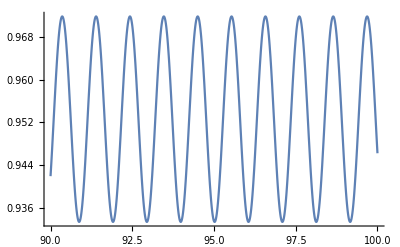

```mathematica
Block[{ω,l,r∞,r0,R∞,Rp∞,ν,μ1,s,μ2,sol},
ω=3;l=3;s=0;
r∞=100;r0=90;
ν=2I ω;μ1=2I ω;μ2=-(s+1);
R∞=E^(ν(r∞-1))(r∞-1)^μ1(r∞)^(μ2+s+1);
Rp∞=E^((-1+r∞) ν) (-1+r∞)^(-1+μ1) (r∞)^(s+μ2) (-1-s-μ2+r∞ (1+s+μ1+μ2+(-1+r∞) ν));
sol=NDSolve[{R''[r]+((1-2I ω r^2)/(r(r-1)))R'[r]-((l(l+1)+1/r)/(r(r-1)))R[r]==0,R[90]==Rationalize[0.91853592036,0]-I Rationalize[0.208634312845,0],R[100]==-Rationalize[0.731491992777,0]-I Rationalize[0.600201441912,0]},R,{r,r0,r∞}];
Plot[Evaluate[(Abs[R[r]]/.sol)],{r,90,100}]
]
```